```mathematica
2 + 2
```

4

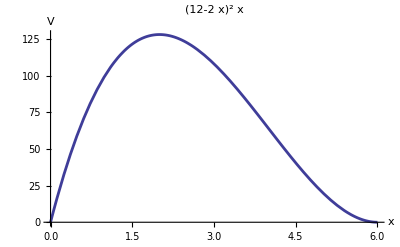

```mathematica
Plot[x (12-2 x)^2,{x,0,6},AxesLabel->{x,V},PlotLabel->x (12-2 x)^2,BaseStyle->{FontFamily->"Helvetica",FontSize->12}, PlotStyle->Thickness[0.005]]
```

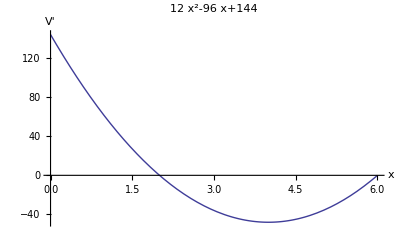

```mathematica
Plot[144-96 x+12 x^2,{x,0,6},AxesLabel->{x,V'},PlotLabel->144-96 x+12 x^2,BaseStyle->{FontFamily->"Helvetica",FontSize->14}]
```

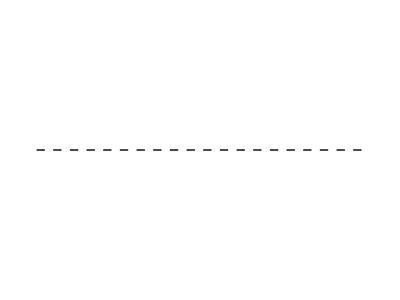

```mathematica
(* Metal sheet horizontal flap cuts. *)
c1 = Graphics[{Dashing[{0.015, 0.015}], Line[{{0,1.5}, {6,1.5}}]}]
```

```mathematica
c2 = Graphics[{Dashing[{0.015, 0.015}], Line[{{0,4.5}, {6,4.5}}]}]
```

-Graphics-

```mathematica
c3 = Graphics[{Dashing[{0.015, 0.015}], Line[{{4.5,0}, {4.5,6}}]}]
```

-Graphics-

```mathematica
c4 = Graphics[{Dashing[{0.015, 0.015}], Line[{{1.5,0}, {1.5,6}}]}]
```

-Graphics-

-Graphics-

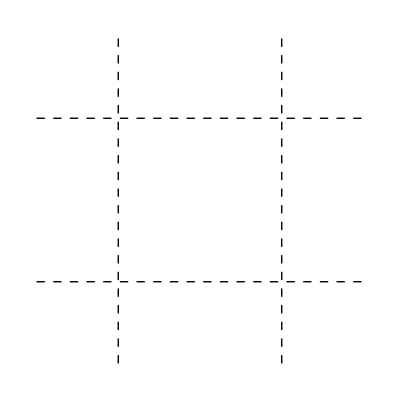

```mathematica
⁃Graphics⁃
Show[c1,c2,c3,c4]
```

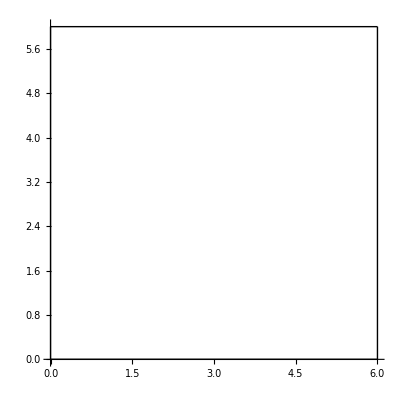

```mathematica
c5 = ParametricPlot[{{t, 0}, {t, 6}, {0, t}, {6, t}}, {t, 0, 6}, Frame->None, PlotStyle->{Black}]
```

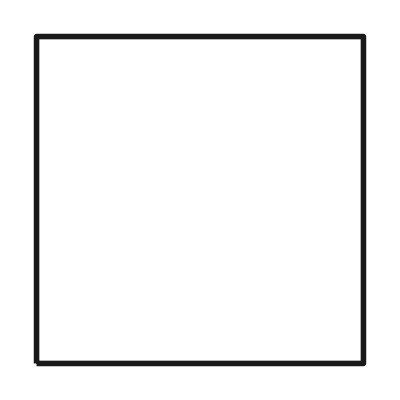

```mathematica
c6 = Show[Graphics[{RGBColor[.1,.1,.1],Thickness[0.01], Line[{{1.5,1.5},{1.5,4.5},{4.5,4.5},{4.5, 1.5},{1.5,1.5}}]}]]
```

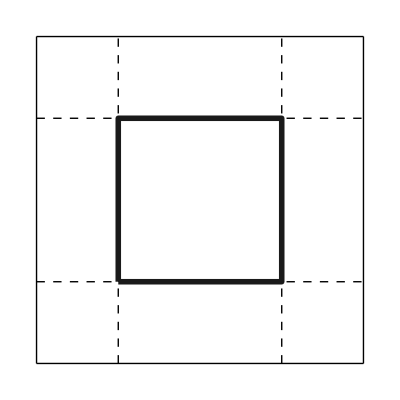

```mathematica
Show[c1,c2,c3,c4,c5,c6]
```

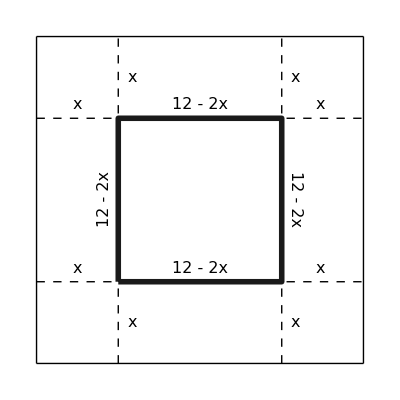

```mathematica
Show[c1,c2,c3,c4,c5,c6,AspectRatio->1.,Epilog->{Text[Style["x", FontSize->16],{5.2,1.75}],Text[Style["x", FontSize->16],{0.75,1.75}],Text[Style["x", FontSize->16],{0.75,4.75}],Text[Style["x", FontSize->16],{5.2,4.75}],Text[Style["12 - 2x", FontSize->16],{3.,1.75}],Text[Style["12 - 2x", FontSize->16],{3.,4.75}],Text[Style["x", FontSize->16],{1.75,0.75}],Text[Style["x", FontSize->16],{4.75,0.75}],Text[Style["x", FontSize->16],{1.75,5.25}],Text[Style["x", FontSize->16],{4.75,5.25}],Text[Style["12 - 2x", FontSize->16],{1.25,2.5},{-1,0},{0,1}],Text[Style["12 - 2x", FontSize->16],{4.75,2.5},{1,0},{0,-1}],BaseStyle->{FontSize->14},BaseStyle->{FontSize->14},BaseStyle->{FontSize->14},BaseStyle->{FontSize->14},BaseStyle->{FontSize->14},BaseStyle->{FontSize->14},BaseStyle->{FontSize->14},BaseStyle->{FontSize->14},BaseStyle->{FontSize->14},BaseStyle->{FontSize->14},BaseStyle->{FontSize->14},BaseStyle->{FontSize->14}}]
```

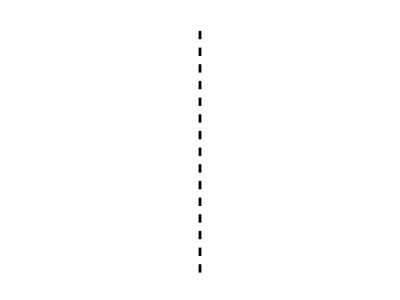

```mathematica
minone = Graphics[{Dashing[{0.015,0.015}], Thickness[0.005], Line[{{1,0}, {1, 5}}]}]
```

```mathematica
maxfour = Graphics[{Dashing[{0.015,0.015}], Thickness[0.005],Line[{{4,0}, {4, 5}}]}]
```

-Graphics-

```mathematica
maxfour2 = Graphics[{Dashing[{0.015, 0.015}],Thickness[0.005], Line[{{4.2,0}, {4.2, 5}}]}]
```

-Graphics-

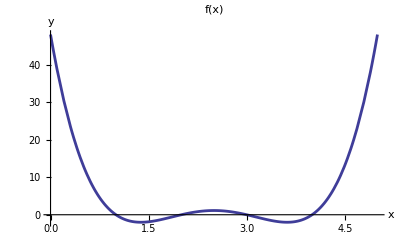

```mathematica
hump1=Plot[(x-1) (2 x-4) (x-3) (x-4),{x,0,5},AxesOrigin->{0,0},AxesLabel->{x,y},PlotLabel->"f(x)",BaseStyle->{FontFamily->"Helvetica",FontSize->14},DisplayFunction->Identity, PlotStyle->Thickness[0.005]]
```

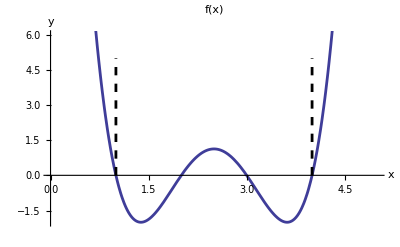

```mathematica
(* humpfunc.eps *)
Show[hump1,minone, maxfour, DisplayFunction -> $DisplayFunction, PlotRange->{-2,6}]
```

```mathematica
hump2=Plot[(x-1) (2 x-4) (x-3) (x-4),{x,0,5},AxesOrigin->{0,0},AxesLabel->{x,y},PlotLabel->"f(x)",BaseStyle->{FontFamily->"Helvetica",FontSize->14},DisplayFunction->Identity, PlotStyle->Thickness[0.005]]
```

-Graphics-

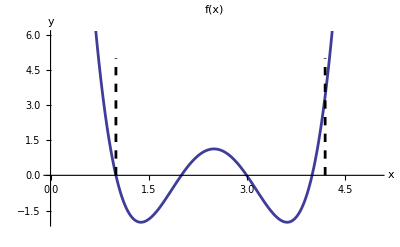

```mathematica
(* humpfunc2.eps *)
Show[hump2,minone, maxfour2, DisplayFunction -> $DisplayFunction, PlotRange->{-2,6}]
```

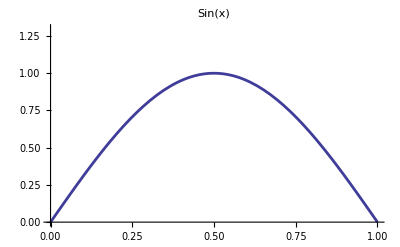

```mathematica
parab=Plot[Sin[π x],{x,0,1},PlotStyle->Thickness[0.005],PlotRange->{0,1.3},PlotLabel->"Sin(x)",BaseStyle->{FontFamily->"Helvetica"}]
```

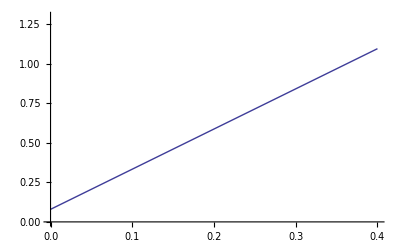

```mathematica
tan1=Plot[π Cos[π 0.2] (x-0.2)+Sin[π 0.2],{x,0,0.4},PlotRange->{0,1.3},BaseStyle->{FontFamily->"Helvetica"}]
```

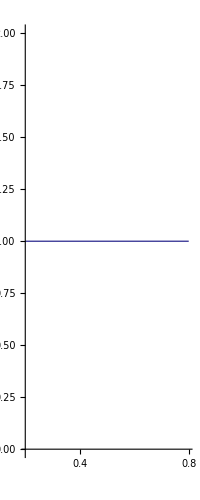

```mathematica
tan2=ParametricPlot[{x,1.},{x,0.2,0.8},BaseStyle->{FontFamily->"Hevetica"}]
```

```mathematica
(* tangents.eps *)
```

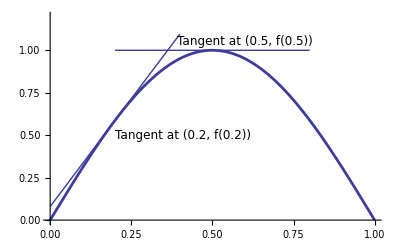

```mathematica
Show[tan1,tan2,parab,Epilog->{Text[Style["   Tangent at (0.5, f(0.5))",FontSize->12,FontFamily->"Helvetica"],{0.6,1.05}],Text[Style["Tangent at (0.2, f(0.2))",FontSize->12,FontFamily->"Helvetica"],{0.2,0.5},{-1,0},{1,0}]}, PlotRange->{{0,1},{0,1.2}}]
```

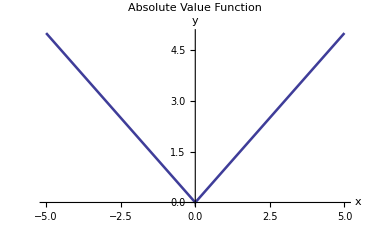

```mathematica
Plot[Abs[x],{x,-5,5},PlotLabel->"                                             Absolute Value Function",BaseStyle->{FontFamily->"Helvetica"},AxesLabel->{x,y}, PlotStyle->Thickness[0.005]]
```

```mathematica
piecewiseLin[x_] := Module[{}, If[x < 0, 1, If[x<3, 1 + x, If[x<5, 4 + (3-x), 2]]]]
```

```mathematica
(* piecewise.eps *)
```

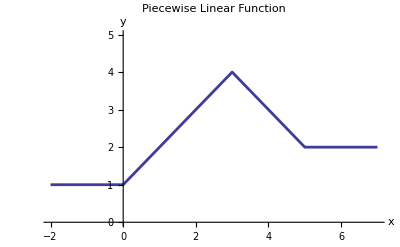

```mathematica
Plot[piecewiseLin[x],{x,-2,7},AxesOrigin->{0,0},PlotRange->{0,5},PlotLabel->"              Piecewise  Linear  Function",BaseStyle->{FontFamily->"Helvetica"},AxesLabel->{x,y}, PlotStyle->Thickness[0.005]]
```

```mathematica
discont[x_] := Module[{}, If[x<0, 0, If[x < 5, x, If[x<10, 7, 0]]]]
```

```mathematica
lin1[x_] := x
```

```mathematica
lin2[x_] := 7
```

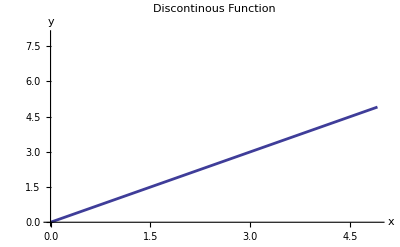

```mathematica
d1=Plot[lin1[x],{x,0,4.91},AxesOrigin->{0,0},PlotRange->{0,8},PlotPoints->50,PlotLabel->"                       Discontinous   Function",BaseStyle->{FontFamily->"Helvetica"},AxesLabel->{x,y}, PlotStyle->Thickness[0.005]]
```

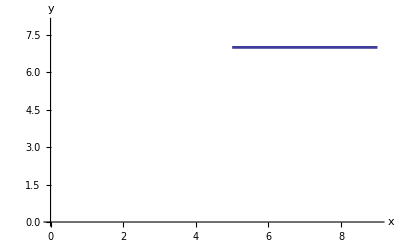

```mathematica
d2=Plot[lin2[x],{x,5,9},AxesOrigin->{0,0},PlotRange->{0,8},PlotPoints->50,AxesLabel->{x,y}, PlotStyle->Thickness[0.005]]
```

```mathematica
(* discont.eps *)
```

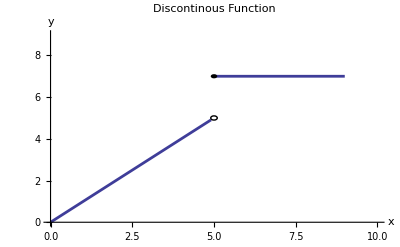

```mathematica
Show[d1,d2, PlotRange->{{0,10},{0,9}},Epilog->{Circle [{5,5},0.1], Disk[{5,7}, 0.1]}]
```

```mathematica
(* linorigin.eps *)
```

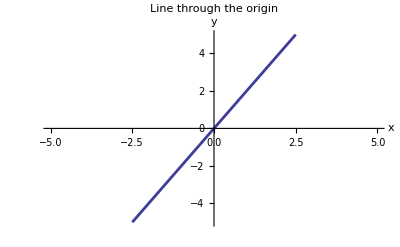

```mathematica
Plot[2 x,{x,-5,5},AxesOrigin->{0,0},PlotRange->{-5,5},PlotPoints->50,PlotLabel->"                                                  Line through the origin",BaseStyle->{FontFamily->"Helvetica"},AxesLabel->{x,y}, PlotStyle->Thickness[0.005]]
```

```mathematica
(* reclin.eps *)
```

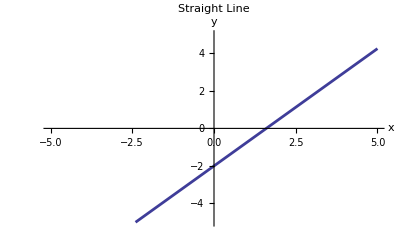

```mathematica
Plot[-2+1.25 x,{x,-5,5},AxesOrigin->{0,0},PlotRange->{-5,5},PlotPoints->50,PlotLabel->"                                         Straight Line",BaseStyle->{FontFamily->"Helvetica"},AxesLabel->{x,y}, PlotStyle->Thickness[0.005]]
```

```mathematica
s3D = Plot3D[Sin[Pi 0.003 (x^2 + y^2)]  , {x, 0-15,15}, {y, -15, 15}, PlotPoints->40, AxesLabel->{"x", "y", "z"}]
```

-Graphics3D-

```mathematica
<<"VectorAnalysis`"
```

```mathematica
linFunc[x_,y_, x0_,y0_] = Sin[Pi 0.003 (x0^2 + y0^2)]+ Dot[Drop[Grad[Sin[Pi 0.003 (x^2 + y^2)], Cartesian[x,y,z]] ,-1]/. {x->x0,y->y0}, {x - x0,y - y0}]
```

0.0188496 (x-x0) x0 Cos[0.00942478 (x0^2+y0^2)]+0.0188496 (y-y0) y0 Cos[0.00942478 (x0^2+y0^2)]+Sin[0.00942478 (x0^2+y0^2)]

```mathematica
linFunc[a,b,-8,-8]
```

0.934329-0.0537456 (8+a)-0.0537456 (8+b)

```mathematica
p3D = Plot3D[linFunc[x,y, -12,-12], {x,-15,15},{y,-15,15},Mesh->False, HiddenSurface->True]
```

-Graphics3D-

```mathematica
Dot[{1,2}, {3,4}]
```

11

```mathematica
Show[p3D,s3D]
```

-Graphics3D-

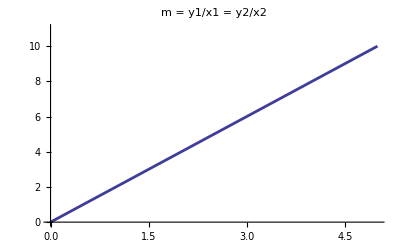

```mathematica
sim1=Plot[2 x,{x,0,5},PlotRange->{0,11},PlotLabel->"m = y1/x1 = y2/x2",BaseStyle->{FontFamily->"Helvetica"}, PlotStyle->Thickness[0.005]]
```

```mathematica
Show[sim, Epilog->{Line[{{0,2}, {2,4}}]}]
```

Show::gtype: Symbol is not a type of graphics.

Show[sim,Epilog→{Line[{{0,2},{2,4}}]}]

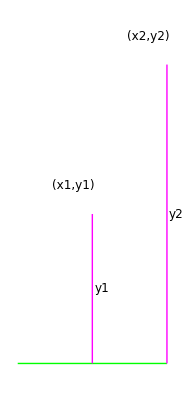

```mathematica
simt1=Graphics[{RGBColor[0,1,0],Line[{{0,0},{4,0}}],RGBColor[1,0,1],Line[{{2,0},{2,4}}],Line[{{4,0},{4,8}}],RGBColor[0,0,0],Text[Style["(x1,y1)",FontSize->12],{1.5,4.75}],Text[Style["(x2,y2)",FontSize->12],{3.5,8.75}],Text[Style["y1",FontSize->12],{2.25,2}],Text[Style["y2",FontSize->12],{4.25,4}],FontFamily->"Helvetica"}]
```

```mathematica
Show[simt1]
```

-Graphics-

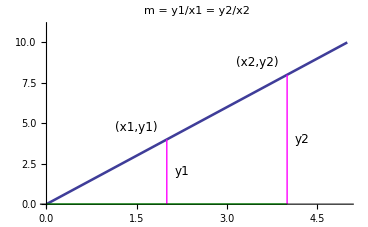

```mathematica
(* simtriangs.eps *)
Show[sim1, simt1]
```

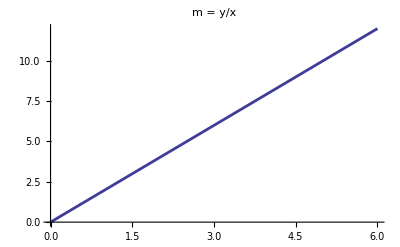

```mathematica
l1=Plot[2 x,{x,0,6},PlotLabel->"m = y/x",BaseStyle->{FontFamily->"Helvetica"}, BaseStyle->{FontSize->20}, PlotStyle->Thickness[0.005]]
```

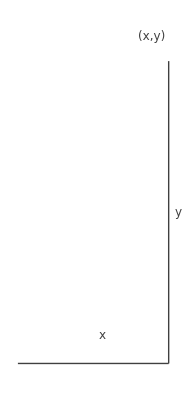

```mathematica
l2=Show[Graphics[{RGBColor[0.25,0.25,0.25],Line[{{4,0},{4,8}}],Line[{{0,0},{4,0}}],Text[Style["y",FontSize->12],{4.25,4}],
Text[Style["x",FontSize->12],{2.25,0.75}],Text[Style["(x,y)", FontSize->12],{3.55,8.65}]}]]
```

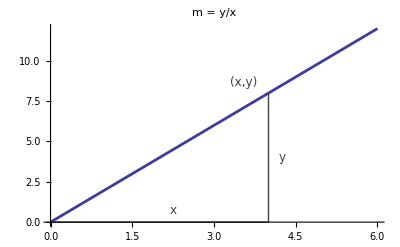

```mathematica
(* linfunc.eps *)
Show[l1,l2]
```

```mathematica
(* absolute.eps *)
```

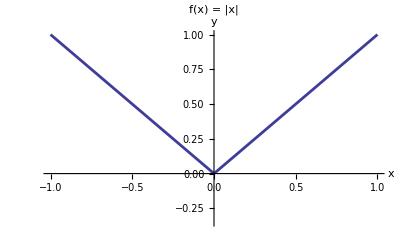

```mathematica
nontan=Plot[Abs[x],{x,-1,1},BaseStyle->{FontSize->10,FontFamily->"Helvetica"},PlotLabel->"                       f(x) = |x|",AxesLabel->{"x","y"},PlotRange->{-0.35,1}, PlotStyle->Thickness[0.005]]
```

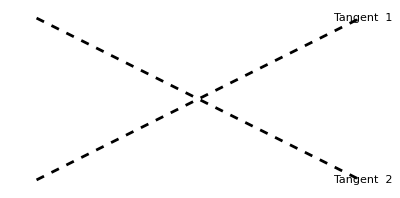

```mathematica
manytangents = Show[Graphics[{Thickness[0.005],{Dashing[{0.015, 0.015}], RGBColor[0,0,0], Line[{{-0.5, -0.25}, {0.5, 0.25}}],
Line[{{-0.5, 0.25}, {0.5, -0.25}}]}, Text["                Tangent  1", {0.51, 0.25}],
Text["                 Tangent  2", {0.51, -0.25}]
}]]
```

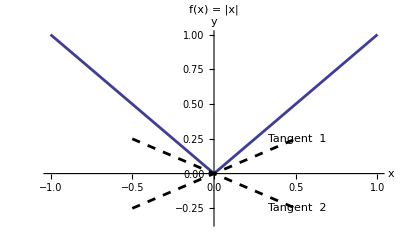

```mathematica
(* nonuniquetang.eps *)
Show[nontan, manytangents]
```

```mathematica
pwconstfunc[x_]  := If[x <2, 1, If[x < 4, 6, If[ x<6, 4, If[x < 8, 10, 12]]]]
```

```mathematica
zerofunc[x_] := 0.0
```

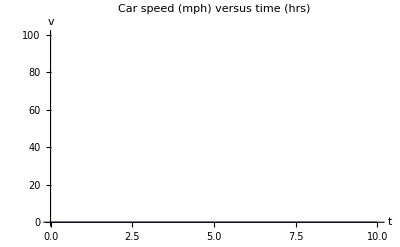

```mathematica
zf=Plot[zerofunc[x],{x,0,10},PlotRange->{0,100},PlotLabel->"        Car speed (mph) versus  time (hrs)",BaseStyle->{FontFamily->"Helvetica",FontSize->12},AxesLabel->{"t","v"}]
```

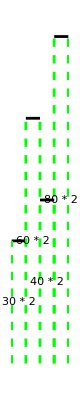

```mathematica
pwcon=Show[Graphics[{Thickness[0.005], Line[{{0,30},{2,30}}],Line[{{2,60},{4,60}}],Line[{{4,40},{6,40}}],Line[{{6,80},{8,80}}],{RGBColor[0,1,0],Dashing[{0.015,0.015}],Line[{{0,0},{0,30}}],Line[{{2,0},{2,60}}],Line[{{4,0},{4,60}}],Line[{{6,0},{6,40}}],Line[{{6,0},{6,80}}],Line[{{8,0},{8,80}}]},Text["30 * 2",{1.,15}],Text["60 * 2",{3.,30}],Text["40 * 2",{5.,20}],Text["80 * 2",{7.,40}],BaseStyle->{FontSize->10},BaseStyle->{FontSize->10},BaseStyle->{FontSize->10},BaseStyle->{FontSize->10}}]]
```

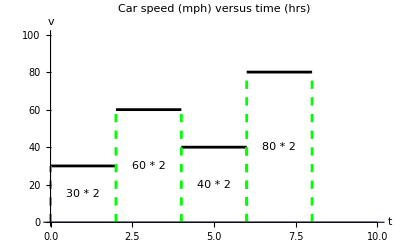

```mathematica
(* pwint.eps *)
Show[zf, pwcon]
```

```mathematica
pwldistfunc[t_] := Module[{}, If[t <2, 30t, If[t<4, 60 + 60 (t-2), If[t < 6,180 +  40(t-4), If[t < 8, 260 + 80( t-6), If[t<10, 420]]]]]]
```

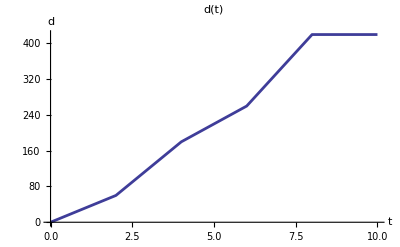

```mathematica
pwl=Plot[pwldistfunc[t],{t,0,10},BaseStyle->{FontFamily->"Helvetica"},PlotLabel->"d(t)",AxesLabel->{"t","d"}, PlotStyle->Thickness[0.005]]
```

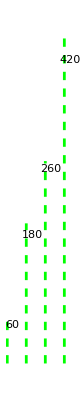

```mathematica
pwlg=Show[Graphics[{Text["60",{2.5,50}],Thickness[0.005], Text["180",{4.6,165}],Text["260",{6.6,250}],Text["420",{8.6,390}],{Dashing[{0.015,0.015}],RGBColor[0,1,0],Line[{{2,0},{2,60}}],Line[{{4,0},{4,180}}],Line[{{6,0},{6,260}}],Line[{{8,0},{8,420}}]},BaseStyle->{FontSize->10},BaseStyle->{FontSize->10},BaseStyle->{FontSize->10},BaseStyle->{FontSize->10}}]]
```

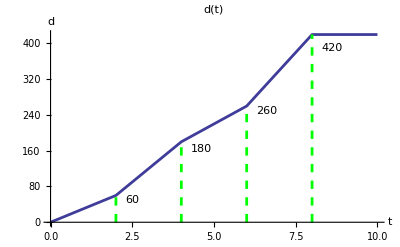

```mathematica
(* pwintd.eps *)
Show[pwl, pwlg]
```

```mathematica
asym[t_] := 60.0  t/( t + 60.0)
```

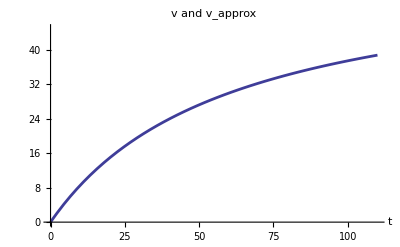

```mathematica
asymg1=Plot[asym[t],{t,0,110},PlotLabel->"v and v_approx",PlotRange->{0,45},BaseStyle->{FontFamily->"Helvetica"},AxesLabel->{"t",""}, PlotStyle->Thickness[0.005]]
```

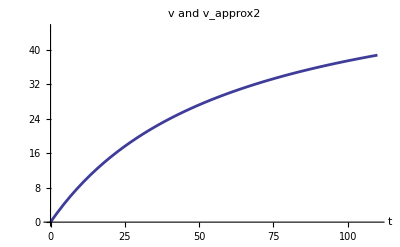

```mathematica
asymg2=Plot[asym[t],{t,0,110},PlotLabel->"v and v_approx2",PlotRange->{0,45},BaseStyle->{FontFamily->"Helvetica"},AxesLabel->{"t",""}, PlotStyle->Thickness[0.005]]
```

```mathematica
makeBars[n_,dx_] := Module[{ddx=dx, nn = n, result={}}, 
For[i=1,i<nn,i++, AppendTo[result, Line[{{i * ddx,0}, {i * ddx, asym[i * ddx]}}]]];
result]
```

```mathematica
makeCaps[n_,dx_] := Module[{ddx = dx, nn = n, result = {}},
For[i=1,i<nn,i++, AppendTo[result, Line[{{(i -1) ddx, asym[(i-1)ddx]}, {i  ddx, asym[(i-1) ddx]}}]]];
result]
```

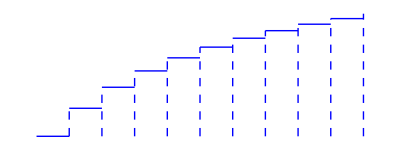

```mathematica
approxg = Show[Graphics[{Dashing[{0.015, 0.015}], 
RGBColor[0,0,1],makeBars[11,10], Dashing[{1.0,0.0}],RGBColor[0,0,1], makeCaps[11,10]}]]
```

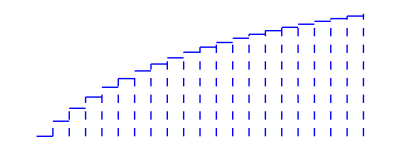

```mathematica
approxg2 = Show[Graphics[{Dashing[{0.015, 0.015}], 
RGBColor[0,0,1],makeBars[21,5], Dashing[{1.0,0.0}],RGBColor[0,0,1], makeCaps[21,5]}]]
```

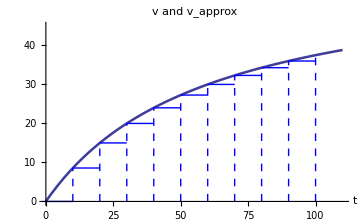

```mathematica
(* pwcapprox.eps *)
Show[asymg1, approxg]
```

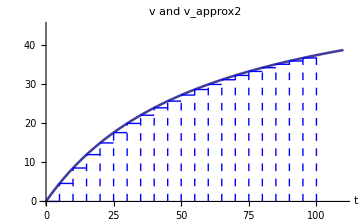

```mathematica
(* pwcapprox2.eps *)
Show[asymg2, approxg2]
```

```mathematica
(* constdist.eps *)
```

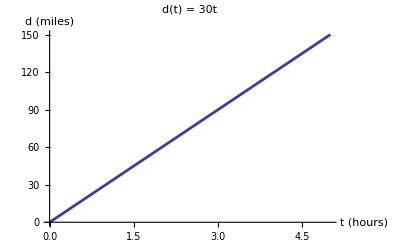

```mathematica
Plot[30 t,{t,0,5},PlotLabel->"d(t) = 30t",PlotRange->{0,150},BaseStyle->{FontFamily->"Helvetica"},AxesLabel->{"t (hours)","d (miles)"}, PlotStyle->Thickness[0.005]]
```

```mathematica
(* constvelc.eps *)
```

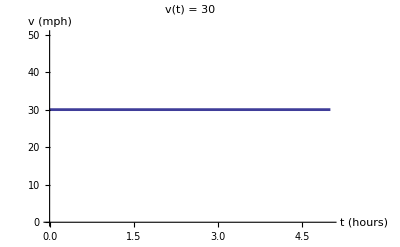

```mathematica
Plot[30,{t,0,5},PlotLabel->"v(t) = 30",PlotRange->{0,50},BaseStyle->{FontFamily->"Helvetica"},AxesLabel->{"t (hours)","v (mph)"}, PlotStyle->Thickness[0.005]]
```

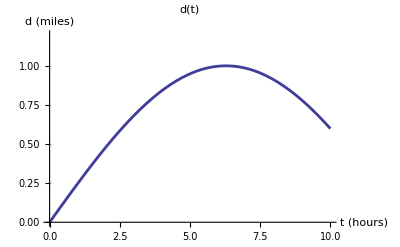

```mathematica
distg=Plot[Sin[0.25 t],{t,0,10},PlotLabel->"d(t)",PlotRange->{0,1.2},BaseStyle->{FontFamily->"Helvetica"},AxesLabel->{"t (hours)","d (miles)"}, PlotStyle->Thickness[0.005]]
```

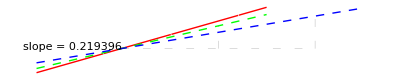

```mathematica
appderivg=Show[Graphics[{{Dashing[{1.,0.}],RGBColor[1,0,0],Line[{{0.25,Sin[0.25 2]+(0.25-2.) Cos[0.25 2] 0.25},{5.,Sin[0.25 2]+(5-2.) Cos[0.25 2] 0.25}}]},{Dashing[{0.015,0.015}],RGBColor[0,1,0],Line[{{0.25,Sin[0.25 2]+((0.25-2.) (Sin[0.25 4.]-Sin[0.25 2]))/2.},{5.,Sin[0.25 2]+((5-2.) (Sin[0.25 4.]-Sin[0.25 2]))/2.}}]},{Dashing[{0.015,0.015}],RGBColor[0,0,1],Line[{{0.25,Sin[0.25 2]+((0.25-2.) (Sin[0.25 6.]-Sin[0.25 2]))/4.},{7.,Sin[0.25 2]+((7-2.) (Sin[0.25 6.]-Sin[0.25 2]))/4.}}]},{RGBColor[0,0,0],Dashing[{0.014,0.025}],Thickness[0.0001],Line[{{2.,Sin[0.25 2.]},{6.,Sin[0.25 2.]}}],Line[{{4.,Sin[0.25 2.]},{4.,Sin[0.25 4.]}}],Line[{{6.,Sin[0.25 2.]},{6.,Sin[0.25 6.]}}]},Text["slope = 0.219396",{1.,0.5}],BaseStyle->{FontSize->8,FontFamily->"Helvetica"}}]]
```

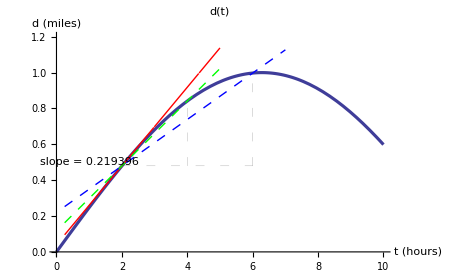

```mathematica
(* distancepoint.eps *)
Show[distg, appderivg]
```

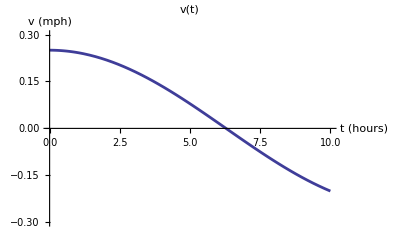

```mathematica
velocg=Plot[0.25 Cos[0.25 t],{t,0,10},PlotLabel->"v(t)",PlotRange->{-0.3,0.3},BaseStyle->{FontFamily->"Helvetica"},AxesLabel->{"t (hours)","v (mph)"}, PlotStyle->Thickness[0.005]]
```

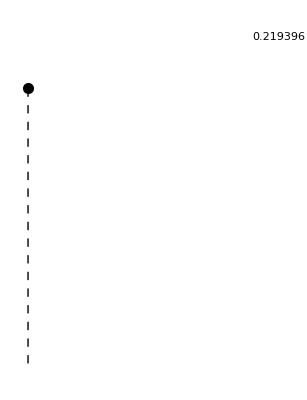

```mathematica
velocpointg=Show[Graphics[{Text[0.25 Cos[0.25 2.],{2.2,0.26}],{PointSize[0.02],Point[{2.,0.25 Cos[0.25 2.]}]},{Dashing[{0.015,0.015}],Line[{{2.,0.},{2.,0.25 Cos[0.25 2.]}}]},BaseStyle->{FontSize->10,FontFamily->"Helvetica"}}]]
```

```mathematica
(* velocitypoint.eps *)
```

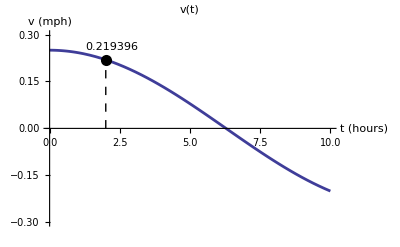

```mathematica
Show[velocg, velocpointg]
```

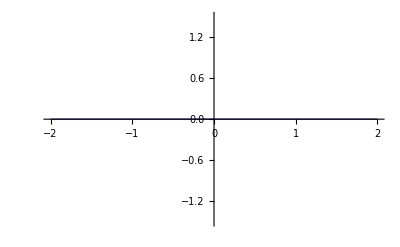

```mathematica
vecg1 = Plot[0, {x,-2,2}, PlotRange->{-1.5,1.5}]
```

```mathematica
<<Graphics`Arrow`
```

General::obspkg: Graphics`Arrow` is now obsolete. The legacy version being loaded may conflict with current Mathematica functionality. See the Compatibility Guide for updating information.

```mathematica
(* basicarrows.eps *)
```

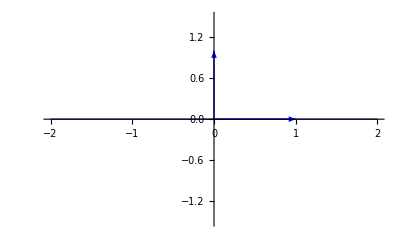

```mathematica
Show[vecg1,Graphics[{RGBColor[0,0,1],Arrow[{0,0},{1,0}], Arrow[{0,0},{0,1}]}]]
```

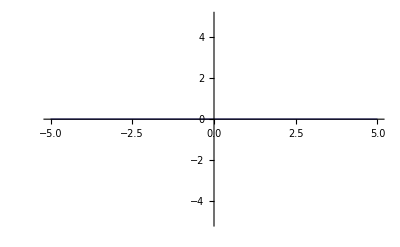

```mathematica
vecg2 = Plot[0, {x,-5,5}, PlotRange->{-5,5}]
```

```mathematica
(* twoarrows.eps *)
```

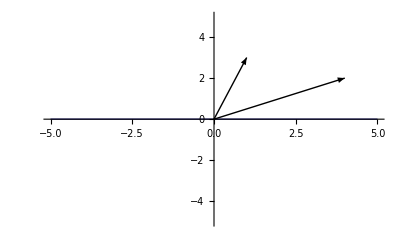

```mathematica
add1=Show[vecg2,Graphics[{Arrow[{0,0},{4,2}], Arrow[{0,0},{1,3}]}]]
```

```mathematica
(* addarrows.eps *)
```

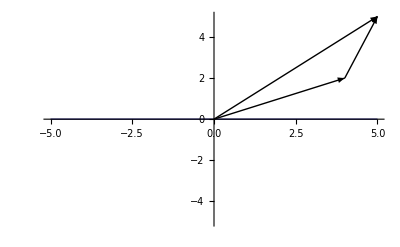

```mathematica
add2=Show[vecg2,Graphics[{Arrow[{0,0},{4,2}], Arrow[{4,2},{5,5}], Arrow[{0,0},{5,5}]}]]
```

```mathematica
(* sinderiv.eps *)
```

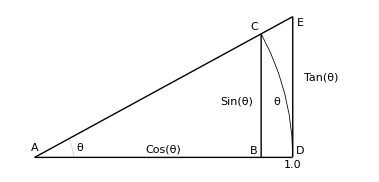

```mathematica
Show[Graphics[{Line[{{0,0},{1,Tan[0.5]}}],Line[{{0,0},{1.,0.}}],Line[{{1.,0.},{1.,Tan[0.5]}}],{Thickness[0.0015],Circle[{0,0},1.,{0.,0.5}]},{RGBColor[1.,1.,1.],Line[{{1.,0.},{1.2,0.}}]},Line[{{Cos[0.5],0},{Cos[0.5],Sin[0.5]}}],Text["A",{0.,0.035}],Text["B",{Cos[0.5]-0.03,0.025}],Text["C",{Cos[0.5]-0.025,Sin[0.5]+0.025}],Text["D",{1.+0.03,0.025}],Text["E",{1.+0.03,Tan[0.5]-0.025}],Text["θ",{0.175,0.035}],Text["1.0",{1.,-0.031}],Text["Cos(θ)",{0.5,0.031}],Text["θ",{Cos[0.25]-0.03,Sin[0.25]-0.031}],Text["Sin(θ)",{Cos[0.5]-0.095,Sin[0.25]-0.031}],Text["Tan(θ)",{1.11,Sin[0.35]-0.031}],{Thickness[0.0001],Circle[{0,0},0.15,{0.,0.5}]},BaseStyle->{FontSize->12,FontFamily->"Helvetica"},BaseStyle->{FontSize->12,FontFamily->"Helvetica"},BaseStyle->{FontSize->12,FontFamily->"Helvetica"},BaseStyle->{FontSize->12,FontFamily->"Helvetica"},BaseStyle->{FontSize->12,FontFamily->"Helvetica"},BaseStyle->{FontSize->12,FontFamily->"Courier"},BaseStyle->{FontSize->8,FontFamily->"Helvetica"},BaseStyle->{FontSize->10,FontFamily->"Courier"},BaseStyle->{FontSize->12,FontFamily->"Courier"},BaseStyle->{FontSize->10,FontFamily->"Courier"},BaseStyle->{FontSize->10,FontFamily->"Courier"}}]]
```

```mathematica
(* oscillating.eps *)
```

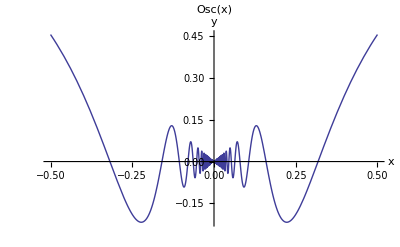

```mathematica
Plot[x Sin[1/x],{x,-0.5,0.5},PlotLabel->"                 Osc(x)",BaseStyle->{FontFamily->"Helvetica"},AxesLabel->{x,y}]
```

```mathematica
(* tangentapprox.eps *)
```

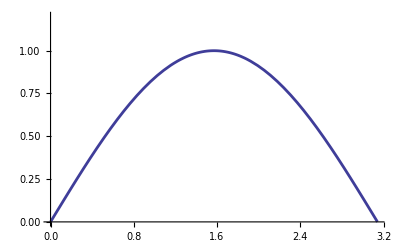

```mathematica
p1 = Plot[Sin[x], {x, 0, Pi}, PlotRange->{0.0, 1.2}, PlotStyle->Thickness[0.005]]
```

```mathematica
t1[x_] := Sin[1.0] + Cos[1.0] (x - 1.0)
```

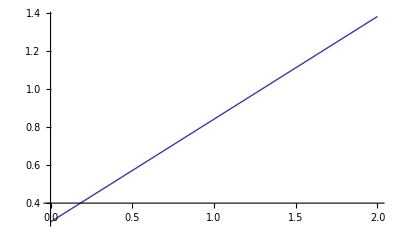

```mathematica
p2 = Plot[t1[x], {x, 0, 2.0}]
```

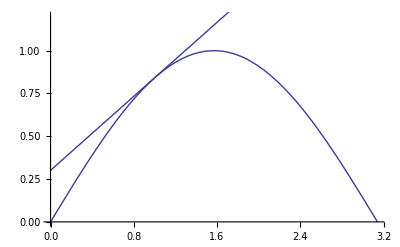

```mathematica
Show[p1,p2]
```

```mathematica
t2[x_] := Sin[1.0] + (Sin[1.25] - Sin[1.0])/(1.25 - 1) (x - 1)
```

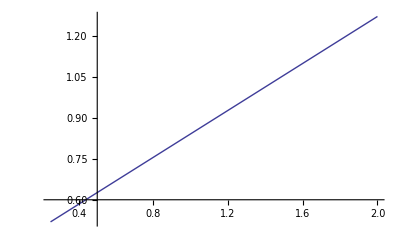

```mathematica
p3 = Plot[t2[x], {x, 0.25, 2.0}]
```

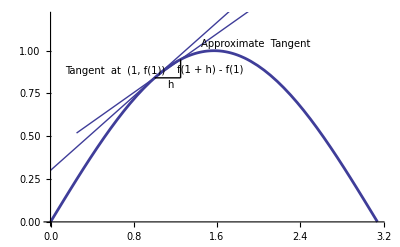

```mathematica
Show[p1,p2,p3,Epilog->{Text[Style["Tangent  at  (1, f(1))",FontSize->10,FontFamily->"Helvetica"],{0.62,0.88}],Text[Style["Approximate  Tangent",FontSize->10,FontFamily->"Helvetica"],{1.97,1.04}],Line[{{1,Sin[1.]},{1.25,Sin[1.]}}],Line[{{1.25,Sin[1.]},{1.25,Sin[1.25]}}],Text[Style["h",FontSize->10,FontFamily->"Helvetica"],{1.15,0.8}],Text[Style["f(1 + h) - f(1)",FontSize->10,FontFamily->"Helvetica"],{1.53,0.89}]}]
```

```mathematica
(* tangentapprox.eps *)
```

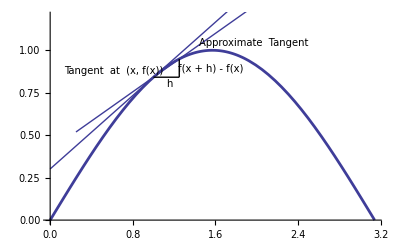

```mathematica
Show[p1,p2,p3,Epilog->{Text[Style["Tangent  at  (x, f(x))",FontSize->10,FontFamily->"Helvetica"],{0.62,0.88}],Text[Style["Approximate  Tangent",FontSize->10,FontFamily->"Helvetica"],{1.97,1.04}],Line[{{1,Sin[1.]},{1.25,Sin[1.]}}],Line[{{1.25,Sin[1.]},{1.25,Sin[1.25]}}],Text[Style["h",FontSize->10,FontFamily->"Helvetica"],{1.15,0.8}],Text[Style["f(x + h) - f(x)",FontSize->10,FontFamily->"Helvetica"],{1.55,0.89}]}]
```